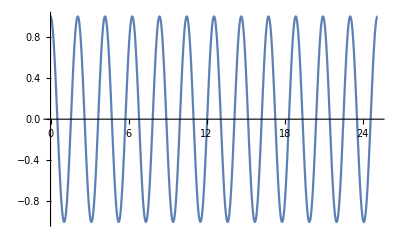

```mathematica
sol= y[x]/. DSolve[{ y''[x] + 9 y[x]==0 , y'[0]==0, y[0]==1}, y[x],x];
Plot[sol,{x,0,8 Pi}]
```

```mathematica
(*-----------------------------------------------------*)
```

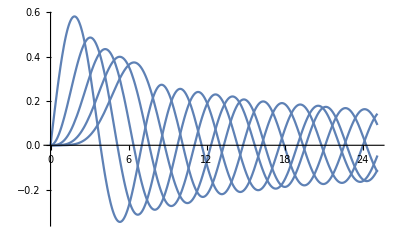

```mathematica
solBes[n_]=y[x]/.DSolve[x^2 y''[x] + x y'[x] + (x^2 -n^2) y[x] ==0 , y[x] , x];
solBes[n_]= solBes[n]/.{C[1]->1, C[2]->0};
Plot[Table[solBes[i],{i,1,5}],{x,0, 8Pi}]
```

```mathematica
(*-----------------------------------------------------*)
```

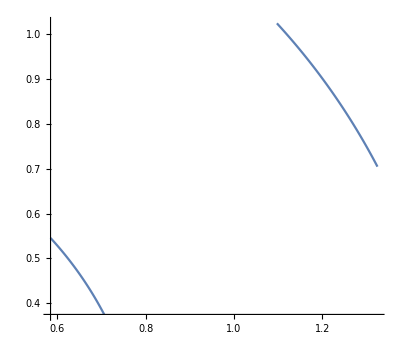

```mathematica
circ1=ParametricPlot[r1=0.8; r2=1.5; { {r1 Cos[th] , r1 Sin[th]}  , {r2 Cos[th] , r2 Sin[th]}    }, {th,28°,43°}]
```

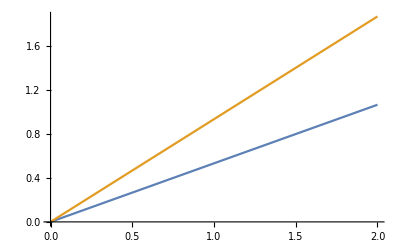

```mathematica
gr2=Plot [ {Tan[28°]x , Tan[43°] x}, {x,0,2}]
```

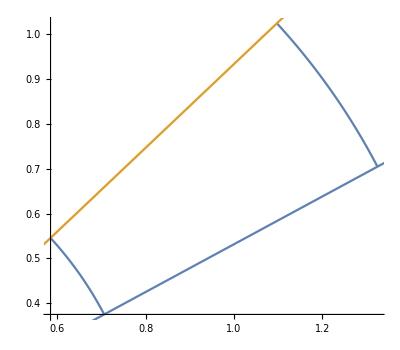

```mathematica
Show[circ1,gr2]
```

```mathematica
c[r_,th1]:=  r Sqrt[1-Cos[th1]^2];
Integrate[ c[r,th1] , {r, 0.8 ,1.5},{th1,28°,43°}]
```

0.122033

```mathematica
Clear[r]


??*Integrate*
```

Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f. 
Integrate[f,{x,y,…}∈reg] integrates over the geometric region reg.

Attributes[Integrate]={Protected,ReadProtected}
 
Options[Integrate]:={Assumptions:>$Assumptions,GenerateConditions→Automatic,PrincipalValue→False}

```mathematica
(*------------------------------------------------*)
```

```mathematica
A={{4,12,-16},{12,37,-43},{-16,-43,98}};
D[j_]:=A[[j,j]] - Sum[ L[[j,k]].Transpose[L[[k,j]]].D[k],
                        {k,1,j-1 } ];
L[i_,j_]:=(1/D[j])(A[[i,j]] - Sum[ L[[i,k]].Transpose[L[[k,j]]].D[k],
                        {k,1,j-1 } ]);
```

SetDelayed::write: Tag D in D[j_] is Protected.